```mathematica
Clear[z, e]
z[x_, n_] = Sum[E^(-x s),{s,0,n}]
e[x_, n_] = Sum[ s E^(-x s),{s,0,n}]/z[x, n]
Manipulate[
Plot[
e[1/y, n], 
{y, 0, 10}, 
PlotRange->Full,
AxesLabel->{Subscript[k, B] T/ϵ, "<s>"}
]
,{{n, 10},1,100}]
```

(ⅇ^(-n x) (-1+ⅇ^(x+n x)))/(-1+ⅇ^x)

-(ⅇ^(x+n x-(1+n) x) (ⅇ^x-ⅇ^((1+n) x)-n+ⅇ^x n))/((-1+ⅇ^x) (-1+ⅇ^(x+n x)))

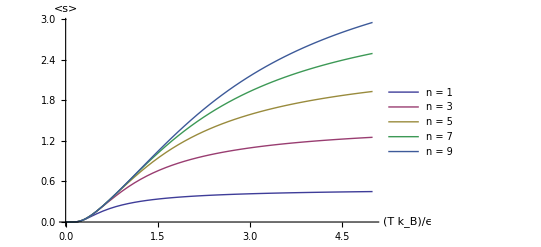

```mathematica
Plot[
Evaluate@Table[e[1/y, n], {n, 1, 10, 2}],
{y, 0, 5}, 
PlotRange->Full,
AxesLabel->{Subscript[k, B] T/ϵ, "<s>"},PlotLegends->Placed[LineLegend[{"n = 1", "n = 3", "n = 5", "n = 7", "n = 9"}],{Left,Top}]
]
```